```mathematica
Clear["`*"]
```

```mathematica
lines=StringSplit[Import["/home/bczhc/fcitx5-log","Text"],"\n"];
```

```mathematica
commits=StringCases[#,RegularExpression["^I([0-9]{4})([0-9]{2})([0-9]{2}) (.*\\.[0-9]+) .*\\[bczhc log] Commit\\(text=(.*)\\)$"] -> {"$1$2$3 $4","$5"}]&/@lines;
commits=#[[1]]&/@Select[commits,#!={}&];
```

```mathematica
commits={DateObject[#[[1]]],#[[2]]}&/@commits//Parallelize;
```

```mathematica
dates=#[[1]]&/@commits;
```

```mathematica
counts=StringLength[#[[2]]]&/@commits;
```

```mathematica
data=WeightedData[dates,counts]
```

WeightedData[<<30770>>]

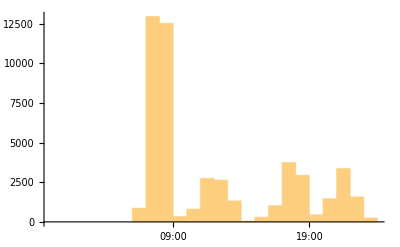

```mathematica
DateHistogram[data,,DateReduction->"Day"]
```